```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## Peak Theory scale-inv.

### Laplacian peak

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,mu>0,kappa>0,n^2-1>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
psin[n_,r_,kW_]=1/sigman[n,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2]

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(2-2 Cos[kW r])/(kW^2 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamman[n_]=sigman[n,kW,As]^2/(sigman[n-1,kW,As]sigman[n+1,kW,As])//Simplify
Rn[n_,kW_]=√3 sigman[n,kW,As]/sigman[n+1,kW,As]//Simplify
```

(√(-1+n^2))/n

(√(3+3/n))/kW

```mathematica
1/x^2 D[(x^2 D[psin[1,x,kW], x]), x]+(sigman[2,kW,As]/sigman[1,kW,As])^2 psin[2,x,kW]//Simplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[2,x,kW], x]), x]+(sigman[3,kW,As]/sigman[2,kW,As])^2 psin[3,x,kW]//Simplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[3,x,kW], x]), x]+(sigman[4,kW,As]/sigman[3,kW,As])^2 psin[4,x,kW]//Simplify
```

0

```mathematica
zetax[x_,mu2_,kappa_]=mu2(1/(1-gamman[3]^2)(psin[1,x/kW,kW]-1/3 Rn[3,kW]^2 sigman[2,kW,As]^2/sigman[1,kW,As]^2 psin[2,x/kW,kW])-kappa^2/(gamman[3](1-gamman[3]^2))(gamman[3]^2 psin[1,x/kW,kW]-1/3 Rn[3,kW]^2 sigman[2,kW,As]^2/sigman[1,kW,As]^2 psin[2,x/kW,kW]))//Simplify
```

-(6 mu2 (-8+6 √2 kappa^2-3 x^2+2 √2 kappa^2 x^2+(8-x^2+√2 kappa^2 (-6+x^2)) Cos[x]-2 (-4+3 √2 kappa^2) x Sin[x]))/x^4

```mathematica
zetaLap[x_,mu_,kappa_]=1/x^2 D[(x^2 D[zetax[x,mu,kappa], x]), x]//Simplify
```

(6 mu (96-72 √2 kappa^2+6 x^2-4 √2 kappa^2 x^2+(-96+42 x^2-x^4+√2 kappa^2 (72-32 x^2+x^4)) Cos[x]-2 x (48-5 x^2+4 √2 kappa^2 (-9+x^2)) Sin[x]))/x^6

```mathematica
Normal[Series[-kW^2 zetaLap[x,mu,kappa](sigman[1,kW,As]/sigman[2,kW,As])^2,{x,0,1}]]
```

mu

```mathematica
zetaLL[x_,mu_,kappa_]=1/x^2 D[(x^2 D[zetaLap[x,mu,kappa], x]), x]//Simplify
```

-1/x^8 6 mu (-72 (40+x^2)+48 √2 kappa^2 (45+x^2)+(2880-1368 x^2+84 x^4-x^6+√2 kappa^2 (-2160+1032 x^2-66 x^4+x^6)) Cos[x]-2 x (-6 (240-34 x^2+x^4)+√2 kappa^2 (1080-156 x^2+5 x^4)) Sin[x])

```mathematica
Normal[Series[kW^4 zetaLL[x,mu,kappa]/mu(sigman[1,kW,As]/sigman[2,kW,As])^2 sigman[2,kW,As]/sigman[4,kW,As],{x,0,1}]]
```

kappa^2

```mathematica
CompactC[x_,mu_,kappa_]=(1-(1+x D[zetax[x,mu,kappa], x])^2)/3//Simplify
```

1/3 (1-1/x^8(-192 mu+144 √2 kappa^2 mu-36 mu x^2+24 √2 kappa^2 mu x^2+x^4+12 mu (16-5 x^2+4 √2 kappa^2 (-3+x^2)) Cos[x]+6 mu x (32-x^2+√2 kappa^2 (-24+x^2)) Sin[x])^2)

```mathematica
xmcond[x_,kappa_]=(D[zetax[x,mu,kappa], x]+x D[D[zetax[x,mu,kappa], x], x])x^5/(12mu)//Simplify
```

64-48 √2 kappa^2+6 x^2-4 √2 kappa^2 x^2+1/2 (-128+52 x^2-x^4+√2 kappa^2 (96-40 x^2+x^4)) Cos[x]-1/2 x (128-11 x^2+3 √2 kappa^2 (-32+3 x^2)) Sin[x]

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk]==0,{x,Min[5/10^logk,5]},WorkingPrecision->50]//Quiet},{logk,-3,2,1/100}];
```

```mathematica
Last[xmList][[2]]100
First[xmList][[2]]
```

2.6592083883523112147945417748657759700612077960189

5.3701421552991077958189118888035944434174892377781

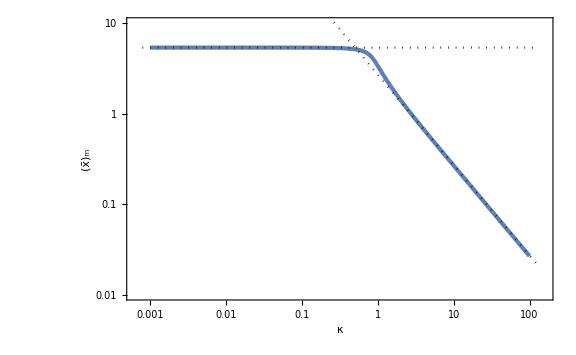

```mathematica
Figxm=Show[ListLogLogPlot[xmList,PlotRange->{{10^-3.2,10^2.2},{0.01,10}},FrameLabel->{κ,Subscript[OverBar[x], "m"]}],LogLogPlot[{2.7/k,5.37},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==267/1000,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

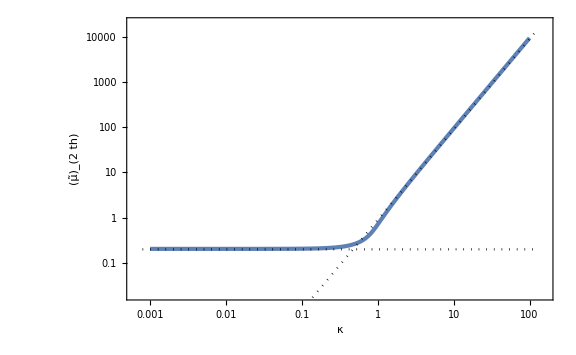

```mathematica
Figmuth=Show[ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]},PlotRange->{{10^-3.2,10^2.2},{0.02,2 10^4}}],LogLogPlot[{0.2,0.9 k^2},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

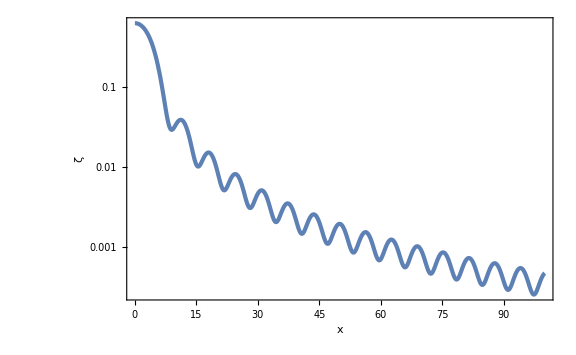

```mathematica
LogPlot[zetax[x,muthint[k],k]/.{k->0.1},{x,0.01,100},PlotRange->Full,FrameLabel->{x,ζ}]
```

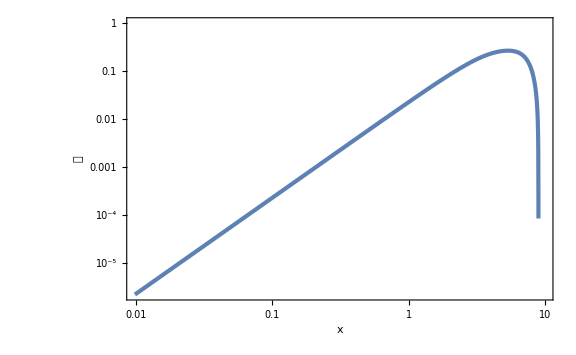

```mathematica
LogLogPlot[CompactC[x,muthint[k],k]/.{k->10^-1},{x,0,10},WorkingPrecision->50,FrameLabel->{x,𝒞}]
```

```mathematica
muthint[10]
```

93.716374899296789123751056186879802506929152269

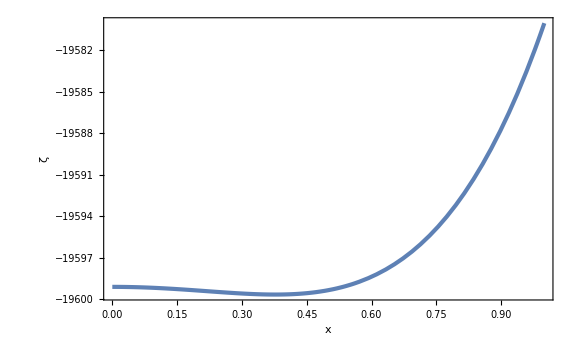

```mathematica
Plot[zetax[x,muthint[k],k]/.{k->10},{x,0,1},WorkingPrecision->50,FrameLabel->{x,ζ}]
```

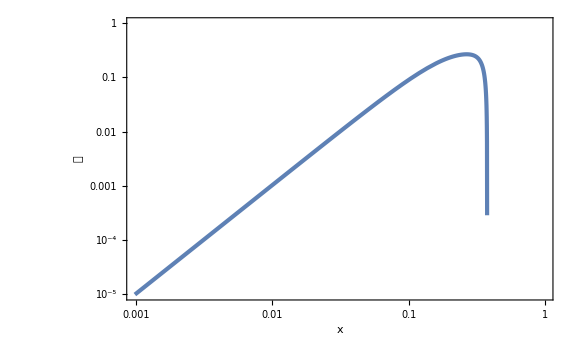

```mathematica
LogLogPlot[CompactC[x,muthint[k],k]/.{k->10},{x,0,1},WorkingPrecision->50,FrameLabel->{x,𝒞}]
```

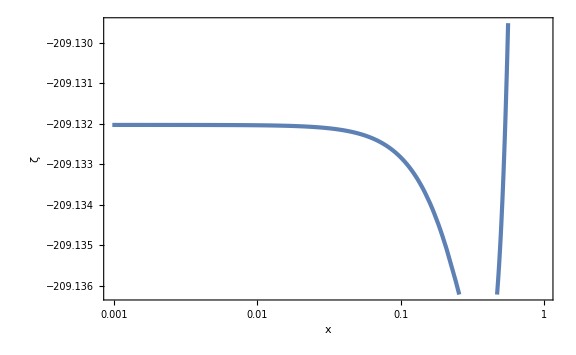

```mathematica
LogLinearPlot[zetax[x,1,k]/.{k->10},{x,0,1},WorkingPrecision->50,FrameLabel->{x,ζ}]
```

```mathematica
Normal[Series[-zetaLap[x,1,100](sigman[1,1,As]/sigman[2,1,As])^2,{x,0,1}]]
```

1

### direct peak

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kUV>0,kIR>0,kUV>kIR,mu>0,kappa>0,n^2-1>0,alpha>0,alpha<1};
```

```mathematica
sigman[n_,kUV_,kIR_,As_]=√(As Integrate[Exp[2n logk],{logk,Log[kIR],Log[kUV]}])//Simplify
```

(√((As (-kIR^(2 n)+kUV^(2 n)))/n))/(√2)

```mathematica
sigma0[kUV_,kIR_,As_]=√(As Integrate[1,{logk,Log[kIR],Log[kUV]}])//Simplify
```

√(As Log[kUV/kIR])

```mathematica
psin[n_,r_,kUV_,kIR_]=1/sigman[n,kUV,kIR,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,kIR,kUV}]//Simplify
psi0[r_,kUV_,kIR_]=1/sigma0[kUV,kIR,As]^2 As Integrate[Sin[k r]/(k r)1/k,{k,kIR,kUV}]//Simplify
```

-1/((-kIR^(2 n)+kUV^(2 n)) r)ⅈ n (kIR^(-1+2 n) (ExpIntegralE[2-2 n,-ⅈ kIR r]-ExpIntegralE[2-2 n,ⅈ kIR r])+kUV^(-1+2 n) (-ExpIntegralE[2-2 n,-ⅈ kUV r]+ExpIntegralE[2-2 n,ⅈ kUV r]))

(-r CosIntegral[kIR r]+r CosIntegral[kUV r]+Sin[kIR r]/kIR-Sin[kUV r]/kUV)/(r Log[kUV/kIR])

```mathematica
psin[1,r,kUV,kIR]//FullSimplify
psin[2,r,kUV,kIR]//FullSimplify
```

-(2 (Cos[kIR r]-Cos[kUV r]))/((kIR^2-kUV^2) r^2)

(2 ⅈ (kIR^3 (ExpIntegralE[-2,-ⅈ kIR r]-ExpIntegralE[-2,ⅈ kIR r])+kUV^3 (-ExpIntegralE[-2,-ⅈ kUV r]+ExpIntegralE[-2,ⅈ kUV r])))/((kIR^4-kUV^4) r)

```mathematica
gamman[n_,kUV_,kIR_]=sigman[n,kUV,kIR,As]^2/(sigman[n-1,kUV,kIR,As]sigman[n+1,kUV,kIR,As])//Simplify
gamma1[kUV_,kIR_]=sigman[1,kUV,kIR,As]^2/(sigma0[kUV,kIR,As]sigman[2,kUV,kIR,As])//Simplify
Rn[n_,kUV_,kIR_]=√3 sigman[n,kUV,kIR,As]/sigman[n+1,kUV,kIR,As]//Simplify
```

(-kIR^(2 n)+kUV^(2 n))/(√(-kIR^(-2+2 n)+kUV^(-2+2 n)) n √((-kIR^(2+2 n)+kUV^(2+2 n))/(-1+n^2)))

(-kIR^2+kUV^2)/(√((-kIR^4+kUV^4) Log[kUV/kIR]))

(√3 √((-kIR^(2 n)+kUV^(2 n)) (1+n)))/(√((-kIR^(2+2 n)+kUV^(2+2 n)) n))

```mathematica
1/x^2 D[(x^2 D[psin[1,x,kUV,kIR], x]), x]+(sigman[2,kUV,kIR,As]/sigman[1,kUV,kIR,As])^2 psin[2,x,kUV,kIR]//FullSimplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[2,x,kUV,kIR], x]), x]+(sigman[3,kUV,kIR,As]/sigman[2,kUV,kIR,As])^2 psin[3,x,kUV,kIR]//FullSimplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[3,x,kUV,kIR], x]), x]+(sigman[4,kUV,kIR,As]/sigman[3,kUV,kIR,As])^2 psin[4,x,kUV,kIR]//FullSimplify
```

0

```mathematica
zetax[x_,mu_,kappa_,alpha_]=mu(1/(1-gamma1[kUV,alpha kUV]^2)(psi0[x/kUV,kUV,alpha kUV]-1/3 Rn[1,kUV,alpha kUV]^2 sigman[1,kUV,alpha kUV,As]^2/sigma0[kUV,alpha kUV,As]^2 psin[1,x/kUV,kUV,alpha kUV])-kappa^2/(gamma1[kUV,alpha kUV](1-gamma1[kUV,alpha kUV]^2))(gamma1[kUV,alpha kUV]^2 psi0[x/kUV,kUV,alpha kUV]-1/3 Rn[1,kUV,alpha kUV]^2 sigman[1,kUV,alpha kUV,As]^2/sigma0[kUV,alpha kUV,As]^2 psin[1,x/kUV,kUV,alpha kUV]))//FullSimplify
```

((1+alpha^2) mu (-2 alpha (-1+alpha^2) (Cos[x]-Cos[alpha x]) Log[alpha]-(-1+alpha^4) x Log[alpha] (alpha x CosIntegral[x]-alpha (x CosIntegral[alpha x]+Sin[x])+Sin[alpha x])+kappa^2 √((-1+alpha^4) Log[alpha]) (-2 alpha Cos[x] Log[alpha]+2 alpha Cos[alpha x] Log[alpha]-(-1+alpha^2) x (alpha x CosIntegral[x]-alpha (x CosIntegral[alpha x]+Sin[x])+Sin[alpha x]))))/(alpha (-1+alpha^4) x^2 Log[alpha] (1-alpha^2+(1+alpha^2) Log[alpha]))

```mathematica
zetaLap[x_,mu_,kappa_,alpha_]=1/x^2 D[(x^2 D[zetax[x,mu,kappa,alpha], x]), x]//Simplify
```

-((mu (Cos[x] ((-1+alpha^2) kappa^2 x^2 √((-1+alpha^4) Log[alpha])+Log[alpha] (-4+x^2+alpha^4 x^2-2 alpha^2 (-2+x^2)+4 kappa^2 √((-1+alpha^4) Log[alpha])-2 kappa^2 x^2 √((-1+alpha^4) Log[alpha])))+Cos[alpha x] (-((-1+alpha^2) kappa^2 x^2 √((-1+alpha^4) Log[alpha]))+Log[alpha] (4+x^2+alpha^4 x^2-4 kappa^2 √((-1+alpha^4) Log[alpha])+2 alpha^2 (-2+x^2 (-1+kappa^2 √((-1+alpha^4) Log[alpha])))))+4 x Log[alpha] (-1+alpha^2+kappa^2 √((-1+alpha^4) Log[alpha])) (Sin[x]-alpha Sin[alpha x])))/((-1+alpha^2) x^4 Log[alpha] (1-alpha^2+(1+alpha^2) Log[alpha])))

```mathematica
Normal[Series[(-zetaLap[x,mu,kappa,alpha])/mu sigma0[kUV,alpha kUV,As]/sigman[2,kUV,alpha kUV,As],{x,0,1}]]//Simplify
```

kappa^2/kUV^2

```mathematica
CompactC[x_,mu_,kappa_,alpha_]=(1-(1+x D[zetax[x,mu,kappa,alpha], x])^2)/3//Simplify
```

1/3 (1-(4 alpha mu Cos[x] Log[alpha] (-1+alpha^2+kappa^2 √((-1+alpha^4) Log[alpha]))-4 alpha mu Cos[alpha x] Log[alpha] (-1+alpha^2+kappa^2 √((-1+alpha^4) Log[alpha]))+x (alpha (-1+alpha^2) x Log[alpha] (1-alpha^2+(1+alpha^2) Log[alpha])-alpha mu ((-1+alpha^2) kappa^2 √((-1+alpha^4) Log[alpha])+Log[alpha] (1-2 alpha^2+alpha^4-2 kappa^2 √((-1+alpha^4) Log[alpha]))) Sin[x]-mu (-((-1+alpha^2) kappa^2 √((-1+alpha^4) Log[alpha]))+Log[alpha] (1+alpha^4+2 alpha^2 (-1+kappa^2 √((-1+alpha^4) Log[alpha])))) Sin[alpha x]))^2/(alpha^2 (-1+alpha^2)^2 x^4 Log[alpha]^2 (1-alpha^2+(1+alpha^2) Log[alpha])^2))

```mathematica
xmcond[x_,kappa_,alpha_]=(D[zetax[x,mu,kappa,alpha], x]+x D[D[zetax[x,mu,kappa,alpha], x], x])1/(mu x^3)//Simplify
```

(-alpha Cos[x] ((-1+alpha^2) kappa^2 x^2 √((-1+alpha^4) Log[alpha])+Log[alpha] (-8+x^2+alpha^4 x^2-2 alpha^2 (-4+x^2)+8 kappa^2 √((-1+alpha^4) Log[alpha])-2 kappa^2 x^2 √((-1+alpha^4) Log[alpha])))-alpha Cos[alpha x] (-((-1+alpha^2) kappa^2 x^2 √((-1+alpha^4) Log[alpha]))+Log[alpha] (8+x^2+alpha^4 x^2-8 kappa^2 √((-1+alpha^4) Log[alpha])+2 alpha^2 (-4+x^2 (-1+kappa^2 √((-1+alpha^4) Log[alpha])))))+x (alpha ((-1+alpha^2) kappa^2 √((-1+alpha^4) Log[alpha])+Log[alpha] (5-6 alpha^2+alpha^4-6 kappa^2 √((-1+alpha^4) Log[alpha]))) Sin[x]+(-((-1+alpha^2) kappa^2 √((-1+alpha^4) Log[alpha]))+Log[alpha] (1+5 alpha^4+6 alpha^2 (-1+kappa^2 √((-1+alpha^4) Log[alpha])))) Sin[alpha x]))/(alpha (-1+alpha^2) x^6 Log[alpha] (1-alpha^2+(1+alpha^2) Log[alpha]))

```mathematica
alphas=10^-5;
```

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk,alphas]==0,{x,3},WorkingPrecision->50]//Quiet},{logk,-3,2,1/100}];
```

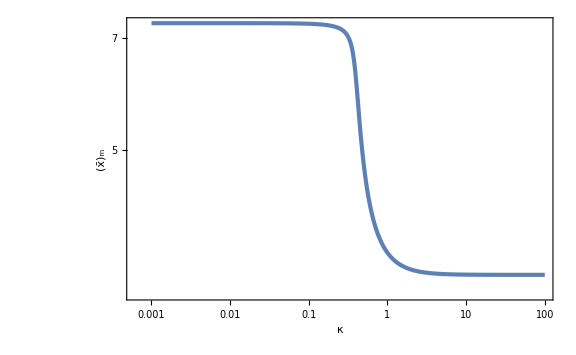

```mathematica
Figxm=ListLogLogPlot[xmList,FrameLabel->{κ,Subscript[OverBar[x], "m"]}]
```

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa,alphas];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==267/1000,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

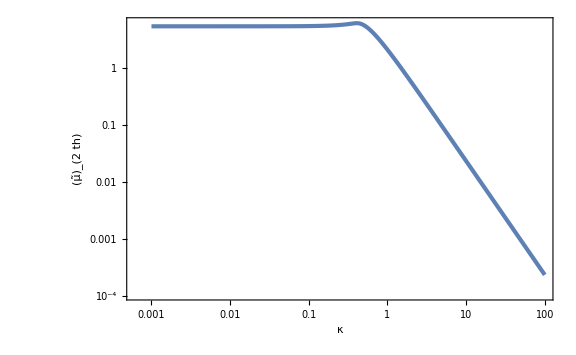

```mathematica
Figmuth=ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]}]
```

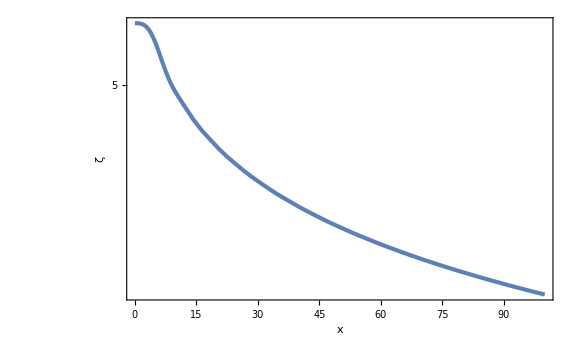

```mathematica
LogPlot[zetax[x,muthint[k],k,alphas]/.{k->0.1},{x,0.01,100},PlotRange->Full,FrameLabel->{x,ζ}]
```

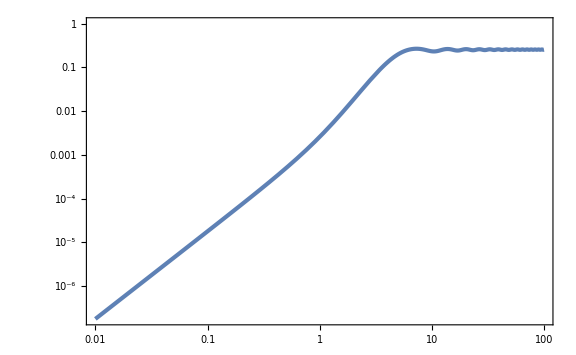

```mathematica
LogLogPlot[CompactC[x,muthint[k],k,alphas]/.{k->10^-1},{x,0.01,100}(*,WorkingPrecision->50,FrameLabel->{x,𝒞}*)]
```

```mathematica
muthint[10]
```

0.0232389954693570941588428796520054860680958007515

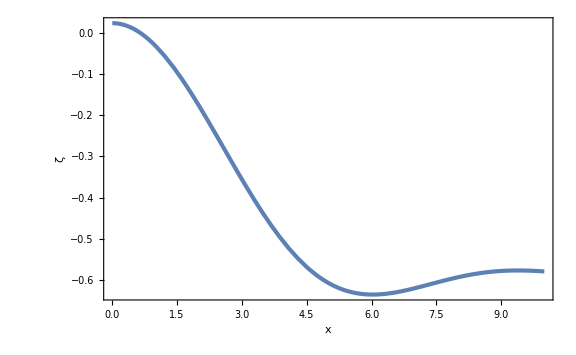

```mathematica
Plot[zetax[x,muthint[k],k,alphas]/.{k->10},{x,0,10},WorkingPrecision->50,FrameLabel->{x,ζ}]
```

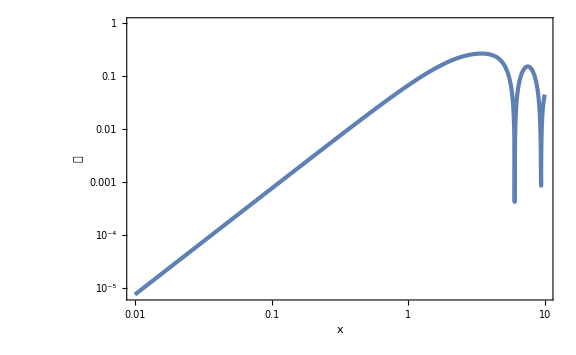

```mathematica
LogLogPlot[Abs[CompactC[x,muthint[k],k,alphas]/.{k->10}],{x,0.01,10},WorkingPrecision->50,FrameLabel->{x,𝒞}]
```

## monochromatic 256 16

```mathematica
npeak=16;
nbias=17;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
kbias=2π nbias/NL
```

π/8

(17 π)/128

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.0242276

0.0237815

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{8,166,0.180717},{33,236,0.250815},{34,22,0.758455},{49,167,0.267825},{53,111,0.276211},{54,247,0.29298},{64,222,0.26255},{118,121,0.312668},{119,96,0.403602},{119,122,0.333786},{142,79,0.379785},{148,6,0.193578},{149,148,0.295193},{165,73,0.412357},{175,25,0.295718},{176,93,0.372455},{209,239,0.185339},{216,60,0.375354},{222,41,0.460632},{244,50,0.228318},{249,89,0.374897},{249,190,0.24422}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

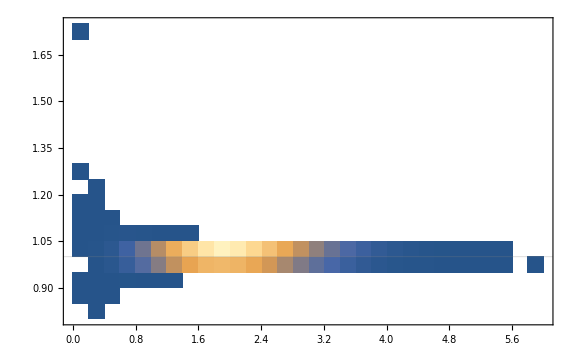

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

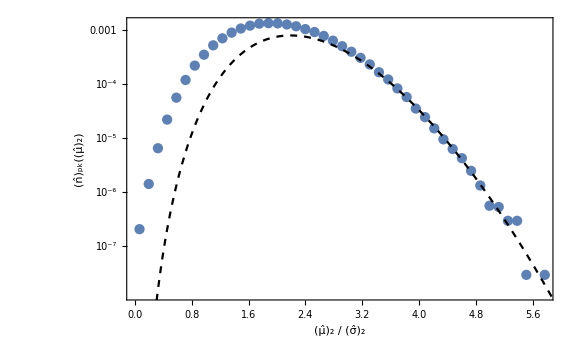

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

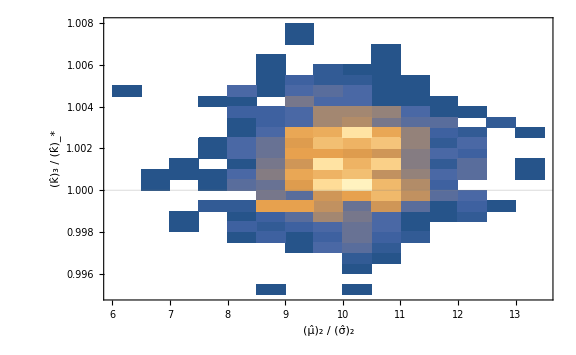

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

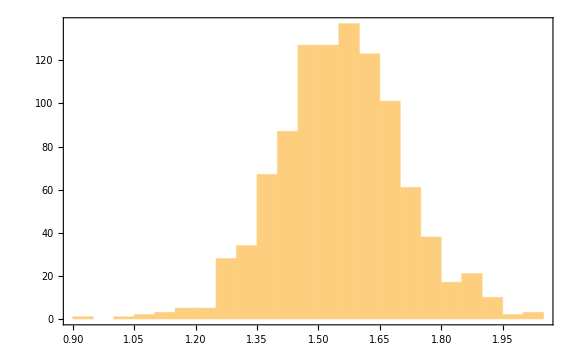

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/20

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

9/10

41/20

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
Length[mu2binning[mu2]]/(Ntot Dmu2)1/NL^3(2π)^3 npeak^3
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

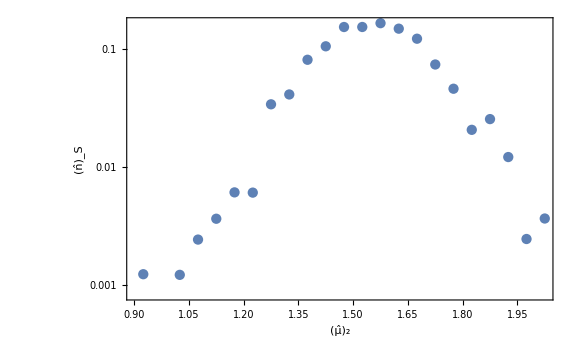

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

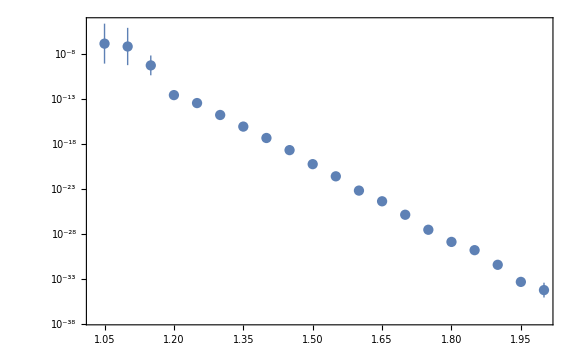

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

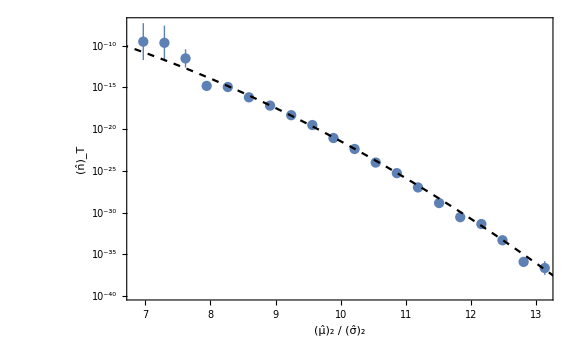

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

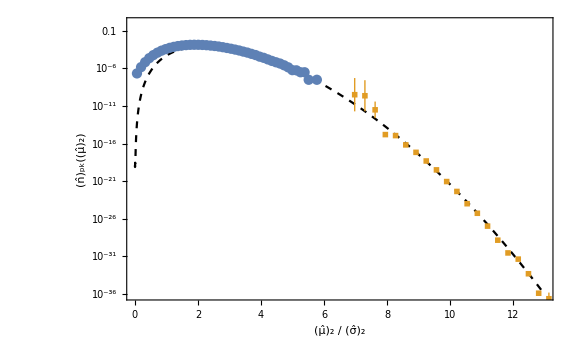

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

### wrong bias

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>".csv"];
Ntot=Length[mukdata]
```

100

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

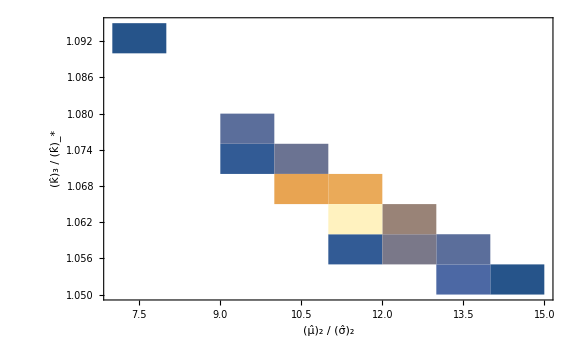

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

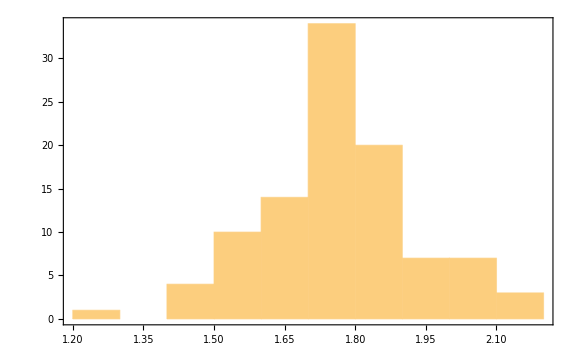

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/10

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

6/5

11/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)(*(Length[mu2binning[mu2]] kbias^3)/(Ntot Dmu2)*)},{mu2,mu2min,mu2max,Dmu2}];
```

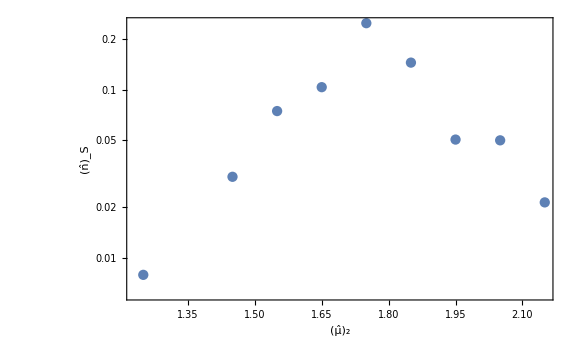

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

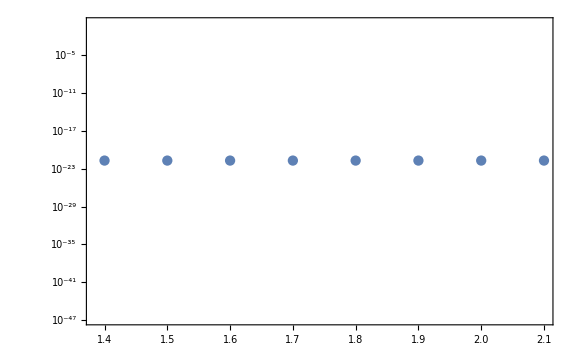

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

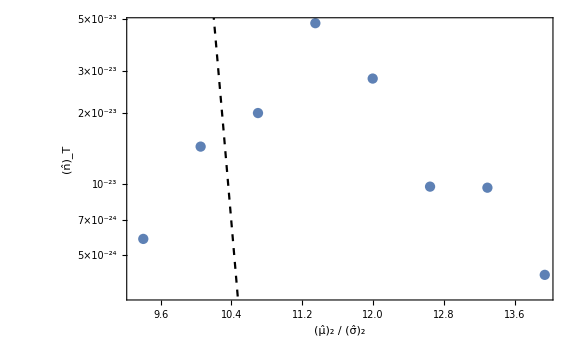

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

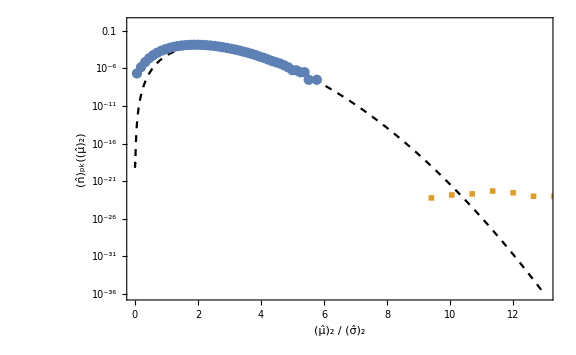

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

### test

```mathematica
mapdata=Import["data/mono_map_0.dat"][[1]];
```

```mathematica
Variance[mapdata]
```

1.01368

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->g[x,y,z]]]
```

-Graphics3D-

```mathematica
powerdata=Import["data/mono_power_0.dat"][[1]];
```

```mathematica
powerList=Table[{i-1,powerdata[[i]]},{i,Length[powerdata]}];
```

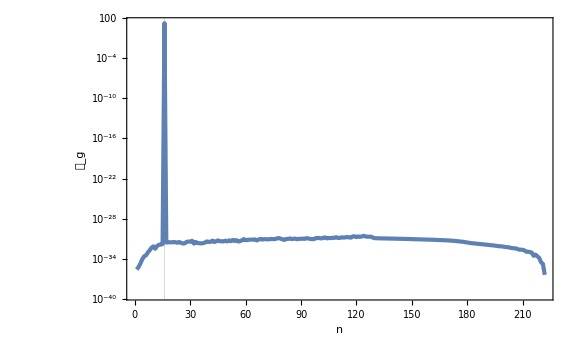

```mathematica
ListLogPlot[powerList,GridLines->{{npeak},None},FrameLabel->{n,Subscript[𝒫, g]}]
```

```mathematica
powerList[[17]]
```

{16,16.2188}

```mathematica
biasedmap=Import["data/mono_biased_0.dat"][[1]];
lapmap=Import["data/mono_laplacian_0.dat"][[1]];
```

```mathematica
shiftedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
lapmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[lapmap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedlap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedlap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

### bias

```mathematica
mapdata=Import["data/mono_bias_laplacian_256_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.0249808

0.0237815

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_bias_peak_256_0.csv"];
```

```mathematica
Select[peakdata,#[[4]]/σ2>10&]
```

{{255,255,1,1.62863,0.391846}}

```mathematica
peak2D=Flatten[Map[{If[#[[2]]>NL/2,ny=#[[2]]-NL,ny=#[[2]]];If[#[[3]]>NL/2,nz=#[[3]]-NL,nz=#[[3]]];
{ny,nz,#[[4]]}}&,Select[peakdata,#[[1]]==255&]],1]
```

{{46,-72,0.24552},{61,-34,0.274946},{75,-67,0.264587},{105,-71,0.241079},{-124,-113,0.478127},{-115,46,0.359853},{-109,4,0.17108},{-106,60,0.300908},{-94,71,0.336816},{-89,-121,0.339492},{-88,-120,0.34782},{-71,-70,0.327307},{-46,116,0.329681},{-42,57,0.318848},{-35,38,0.467295},{-31,24,0.253736},{-25,78,0.299853},{-11,50,0.281742},{-8,87,0.382089},{-1,1,1.62863}}

```mathematica
map2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,mapdata[[NL^2 255+NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

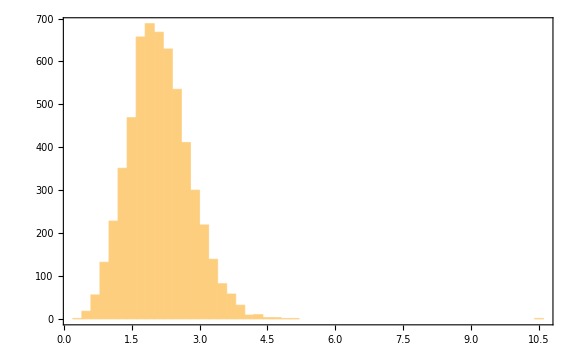

```mathematica
Histogram[peakdata[[All,4]]/σ2,PlotRange->Full]
```

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_256_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

-Graphics-

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[N, L]==256}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

-Graphics-

## monochromatic 256 8

```mathematica
npeak=8;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
```

π/16

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.00162418

0.00148634

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{13,102,0.0435504},{119,133,0.0580749},{167,72,0.067136},{206,75,0.0668344}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

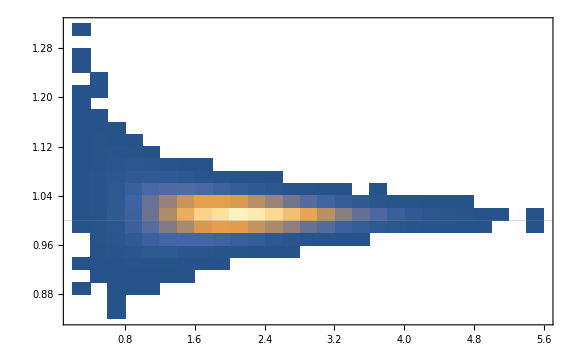

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

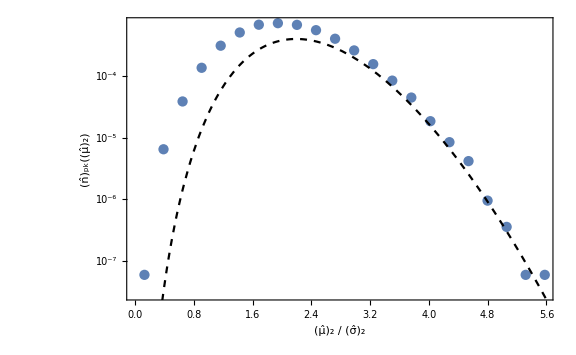

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

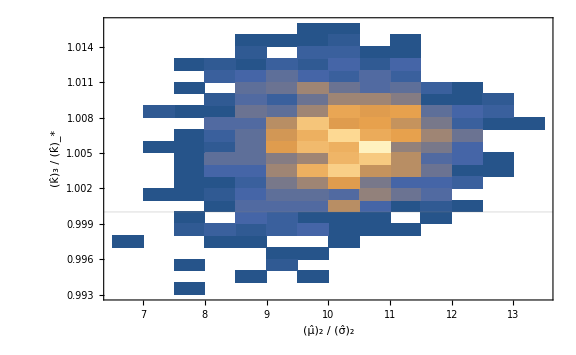

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

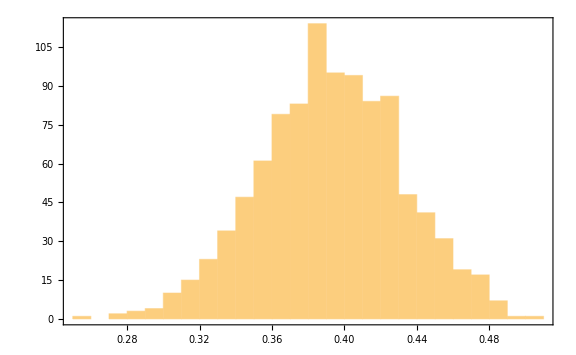

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/100

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

1/4

51/100

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

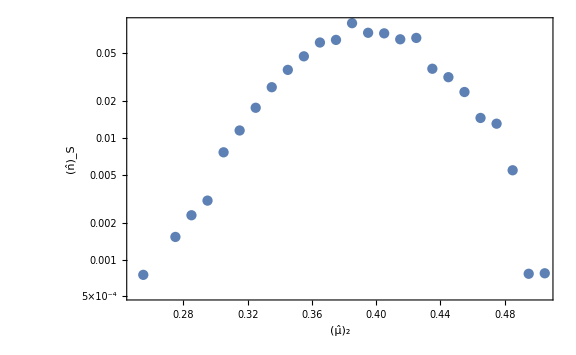

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

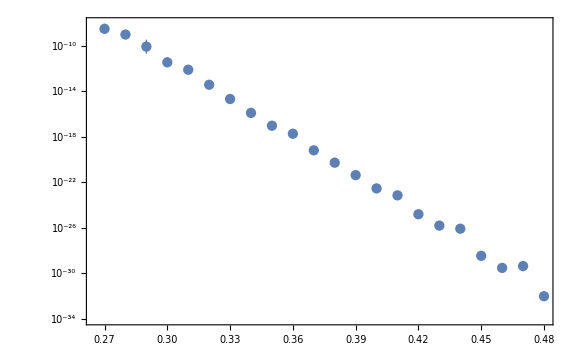

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

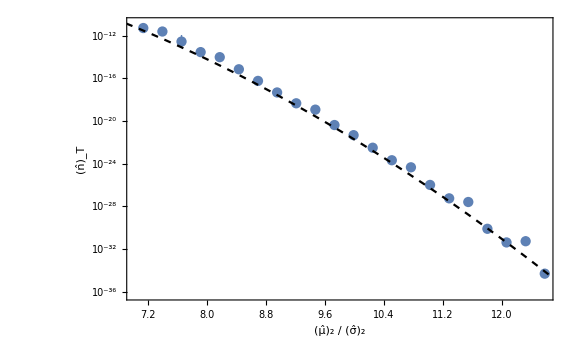

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

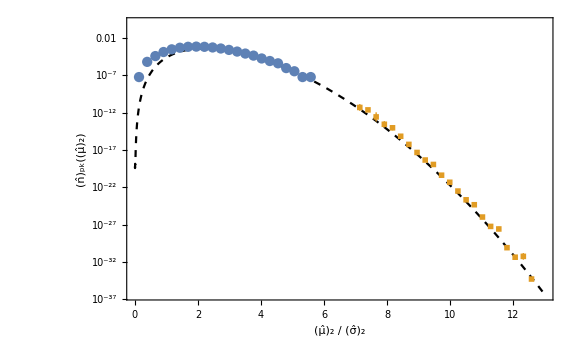

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

## monochromatic 128 16

```mathematica
npeak=2^4;
NL=128;
```

```mathematica
kpeak=2π npeak/NL
```

π/4

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.387642

0.380504

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{6,73,1.07112},{17,119,0.970761},{27,56,1.10484},{32,112,1.01206},{35,87,1.04952},{39,96,1.05852},{44,86,0.529736},{49,14,0.74006},{49,121,0.30645},{53,93,0.826954},{57,77,0.652277},{60,49,1.59837},{67,72,1.84326},{73,30,0.900259},{75,75,1.14675},{83,76,1.45891},{88,46,1.26667},{91,38,0.406844},{105,127,2.03643},{111,74,1.29881},{117,40,1.14442},{120,7,1.14484},{120,39,0.57786},{121,38,0.537725},{123,26,0.843453},{125,45,1.49959},{125,96,0.95891}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

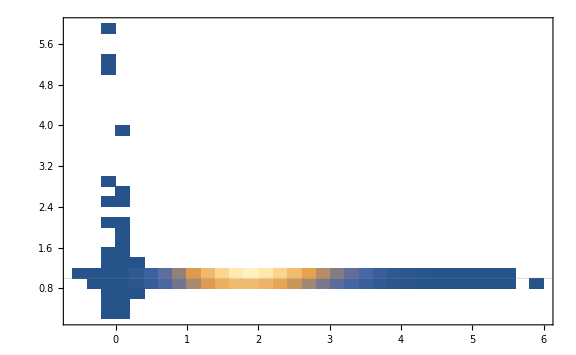

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

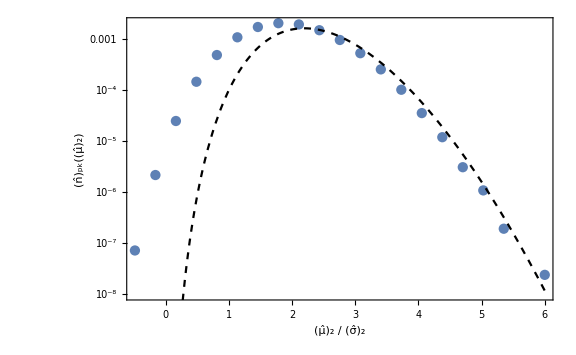

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

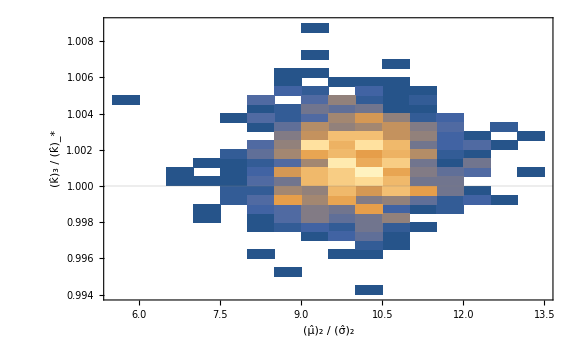

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

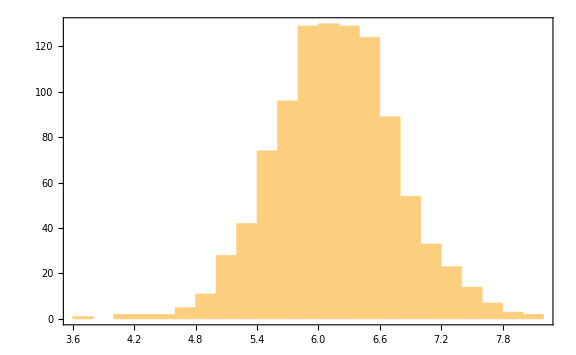

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/5

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

18/5

41/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

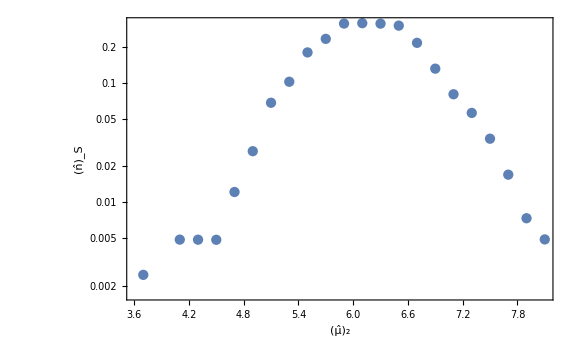

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

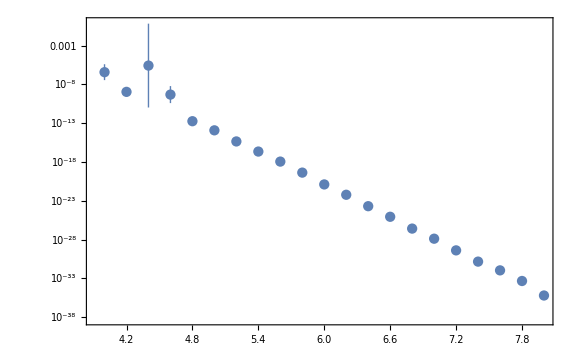

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

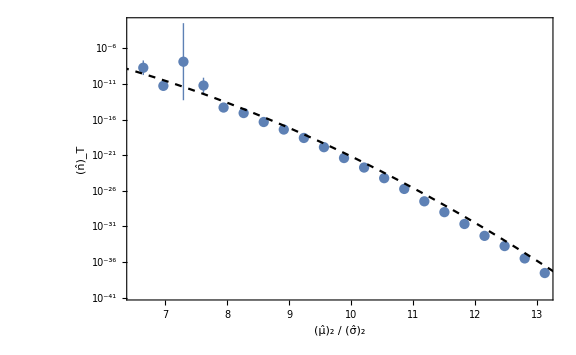

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

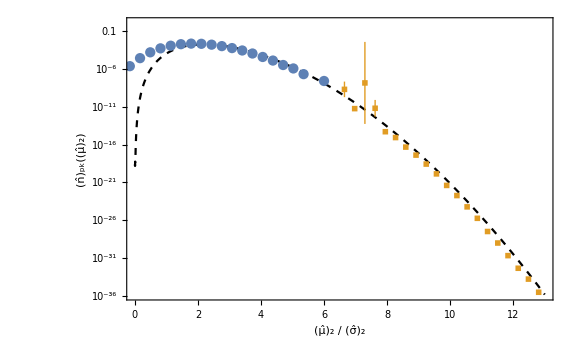

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

## monochromatic 128 8

```mathematica
npeak=2^3;
NL=128;
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.0259868

0.0237815

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{23,114,0.349079},{38,80,0.412598},{51,49,0.517785},{103,38,0.262935},{1,8,0.491576}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

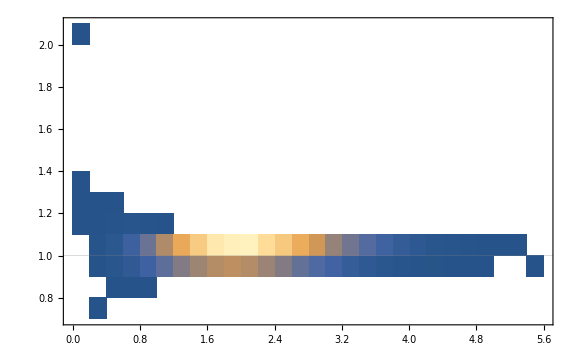

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

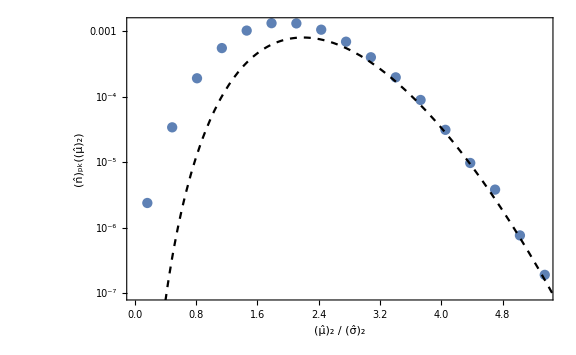

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

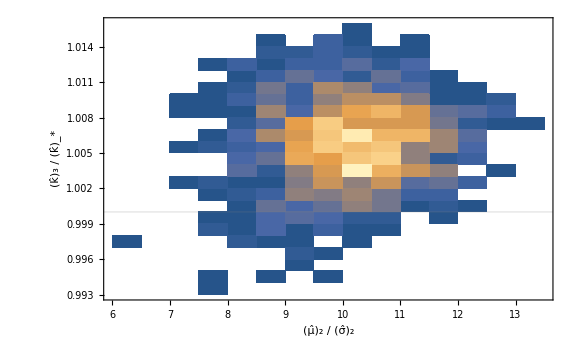

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

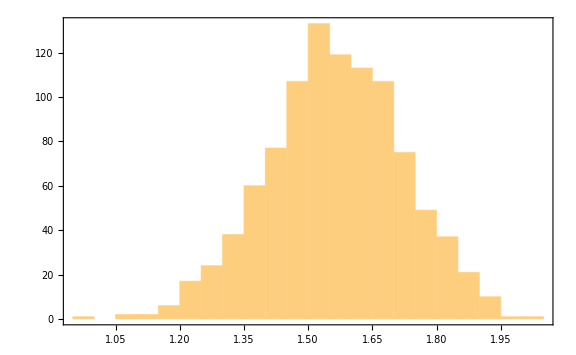

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/20

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

19/20

41/20

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

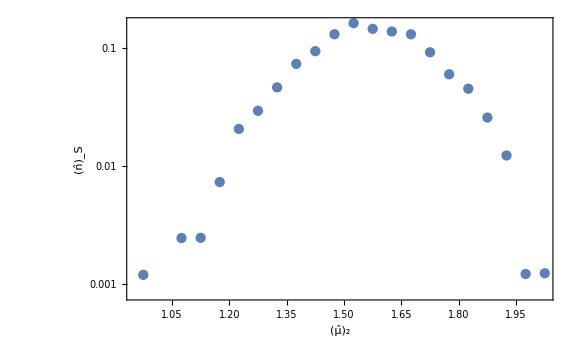

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

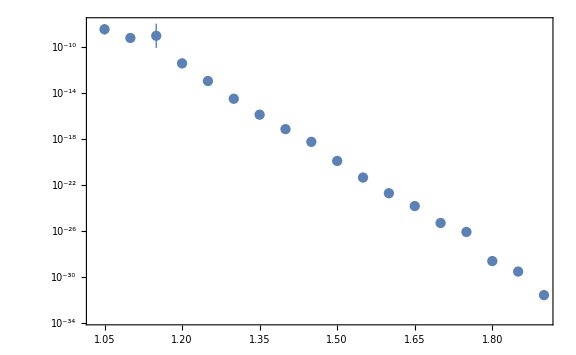

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

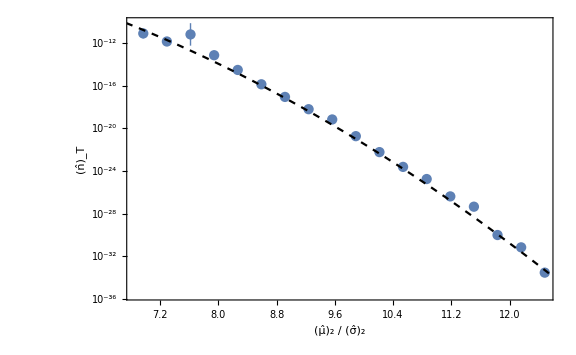

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

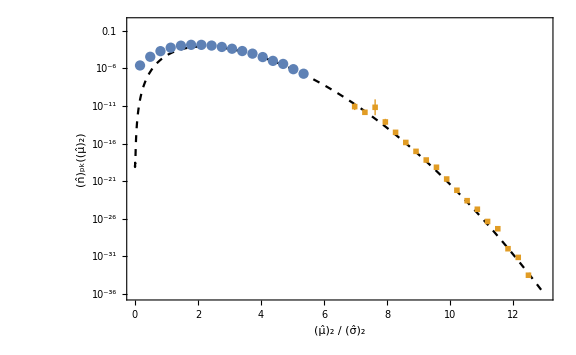

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

## monochromatic 64 8

```mathematica
npeak=2^3;
NL=64;
```

```mathematica
kpeak=2π npeak/NL
```

π/4

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.415791

0.380504

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{8,17,1.94219},{12,57,1.41307},{20,41,1.56269},{26,25,2.07114},{52,20,1.01936},{52,61,1.8886},{54,53,0.939033},{1,4,1.92405}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

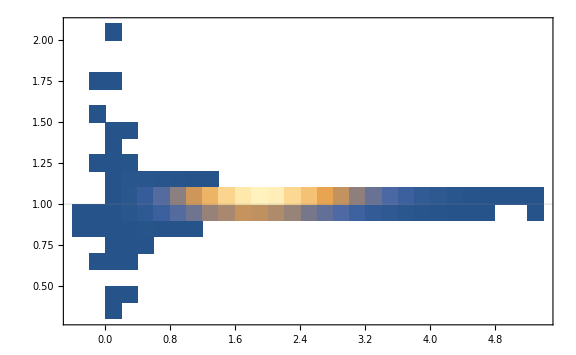

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

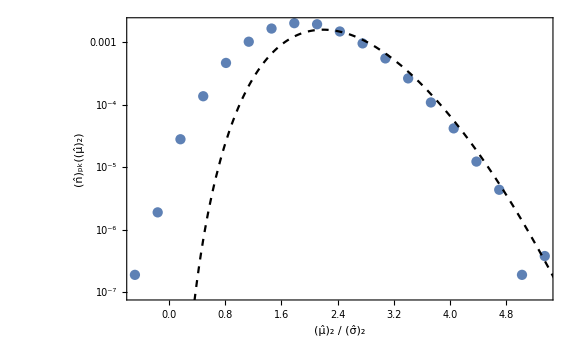

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

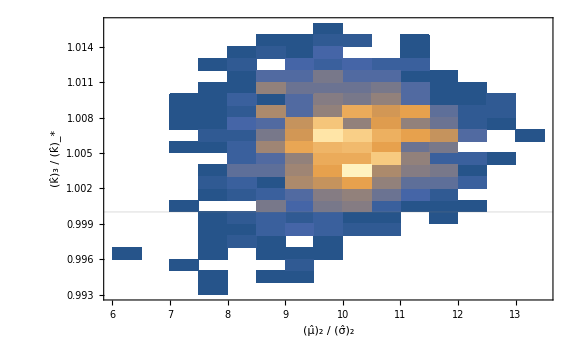

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

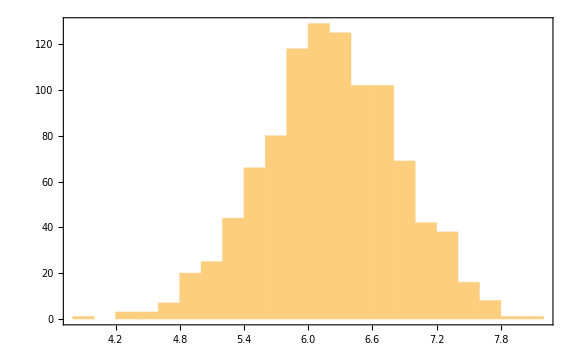

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/5

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

19/5

41/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

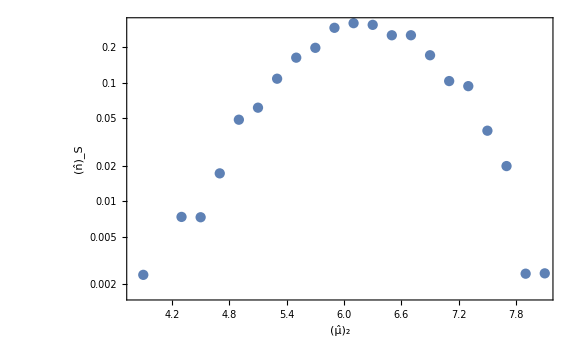

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

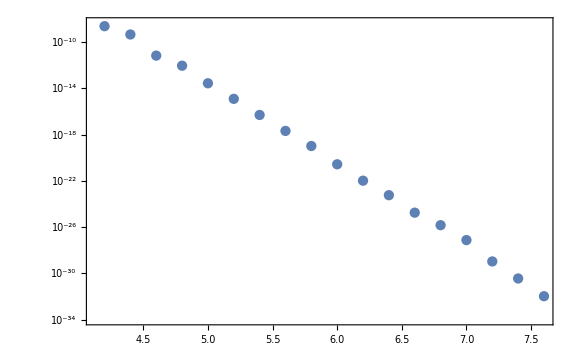

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

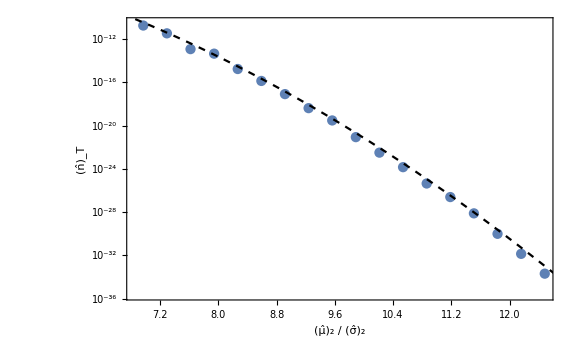

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

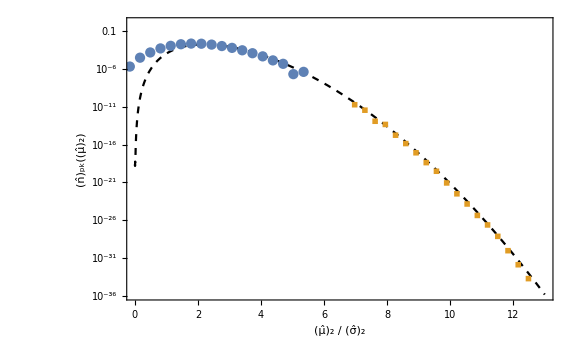

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

## log normal

```mathematica
calPg[lnk_]=1/Sqrt[2π s2] Exp[(-(lnk-lnks)^2)/(2s2)];
```

```mathematica
σn2[n_]=E^(2 n^2 s2)ks^(2n);
```

```mathematica
Simplify[Integrate[Exp[2n lnk]calPg[lnk],{lnk,-∞,∞}]/σn2[n]/.{lnks->Log[ks]},{s2>0,ks>0,n>0}]
```

1

```mathematica
γn=Simplify[σn2[n]/Sqrt[σn2[n-1]σn2[n+1]],{ks>0,n>0,s2>0}]
```

ⅇ^(-2 s2)

```mathematica
Normal[Series[1-γn^2,{s2,0,1}]]
```

4 s2

```mathematica
Normal[Series[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2)),{s2,0,0}]]
```

-(-ν+ξ)^2/(8 s2)+1/4 (-ν^2-ξ^2)

```mathematica
Normal[Series[(1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))])/(1/Sqrt[2π] Exp[-ν^2/2] 1/Sqrt[2π 4s2] Exp[-1/2(ξ-ν)^2/(4s2)]),{s2,0,0}]]
```

ⅇ^(1/4 (ν^2-ξ^2))

```mathematica
npeak=16;
NL=256;
kpeak=(2π npeak)/NL
```

π/8

```mathematica
Sqrt[50 2/(Floor[Sqrt[3]NL]-1)]//N
```

0.475651

```mathematica
1/2 0.48^2(Floor[Sqrt[3]NL]-1)
```

50.9184

### s2 = 0.1

```mathematica
s2=0.1;
```

#### peak

```mathematica
mapdata=Import["data/LN0,1_map_0.csv"][[1]];
```

```mathematica
Length[mapdata]
```

16777216

```mathematica
Variance[mapdata]
```

1.01927

```mathematica
lapdata=Import["data/LN0,1_laplacian_0.csv"][[1]];
```

```mathematica
dn=2^2;
lap3D=Flatten[Table[{nx,ny,nz,lapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[lap3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/LN0,1_peak_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]];
```

```mathematica
lap2D=Flatten[Table[{ny,nz,lapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[lap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=10;
mukList=Flatten[Table[Import["data/LN0,1_peak_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[mu2_,k3_]=2/(6π)^(3/2)σ4^2/(σ2 σ3^3) mu2 k3 f[(mu2 k3^2)/σ4]P13[mu2/σ2,(mu2 k3^2)/σ4];
nmu2PT[mu2_]:=NIntegrate[npkPT[mu2,k3],{k3,0,∞}];
```

```mathematica
σ2^2
```

0.0529267

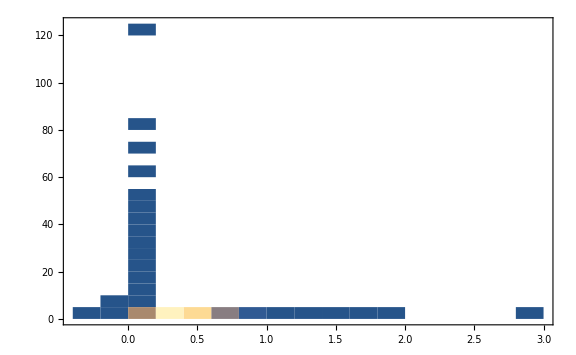

```mathematica
DensityHistogram[mukList,GridLines->{None,{kpeak}}]
```

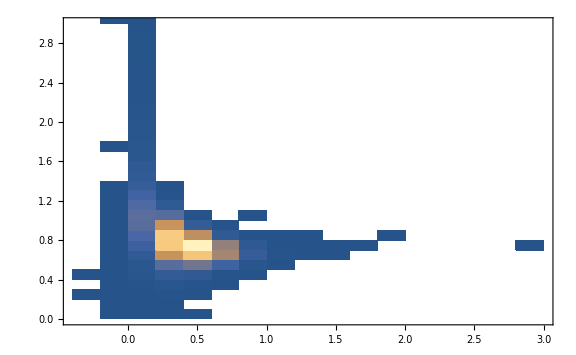

```mathematica
DensityHistogram[mukList,{Automatic,{0.1}},GridLines->{None,{kpeak}},PlotRange->{Full,{0,3}}]
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

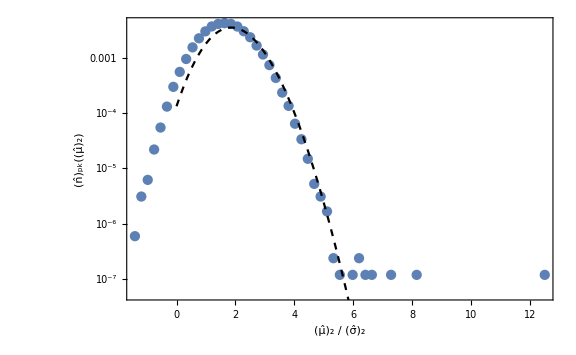

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

```mathematica
HistoList=HistogramList[mukList,{1/10^2}];
```

```mathematica
Dmu2=HistoList[[1,1,2]]-HistoList[[1,1,1]];
Dk3=HistoList[[1,2,2]]-HistoList[[1,2,1]];
mu2min=Mean[HistoList[[1,1,1;;2]]];
k3min=Mean[HistoList[[1,2,1;;2]]];
npkLat=Flatten[Table[{mu2min+Dmu2(i-1),k3min+Dk3(j-1),Log10[HistoList[[2,i,j]]/(Dmu2 Dk3 Nsim NL^3)]},{i,Length[HistoList[[2]]]},{j,Length[HistoList[[2,1]]]}],1];
```

```mathematica
Show[ListDensityPlot[npkLat,PlotLegends->Automatic,PlotRange->{{0,1},{0,4}},PlotRangePadding->None],
ContourPlot[Log10[npkPT[mu2,k3]],{mu2,0,2},{k3,0,5},ContourShading->None,Contours->{-1,-2,-3,-4},PlotRange->Full]]
```

-Graphics-

#### importance sampling

```mathematica
mukdata=Import["data/LN_muk_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

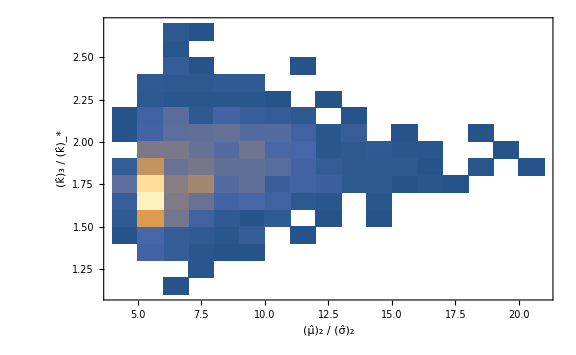

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

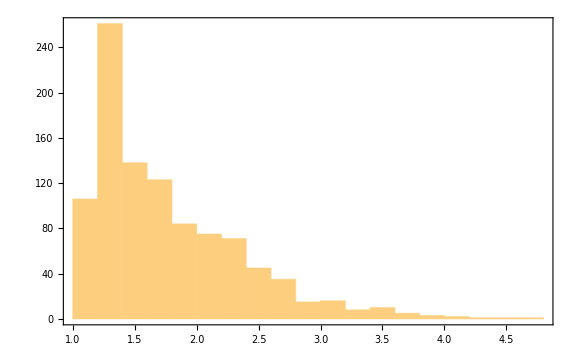

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/5

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

1

24/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

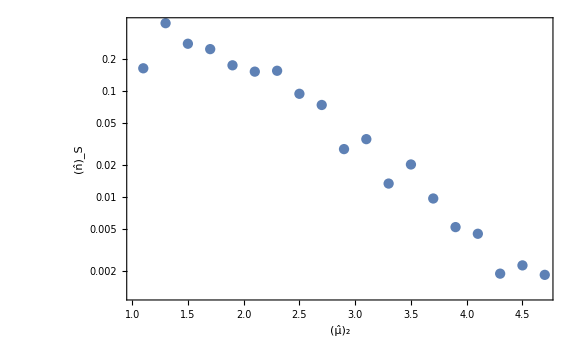

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

General::munfl: Exp[-853.784] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1501.61] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2134.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

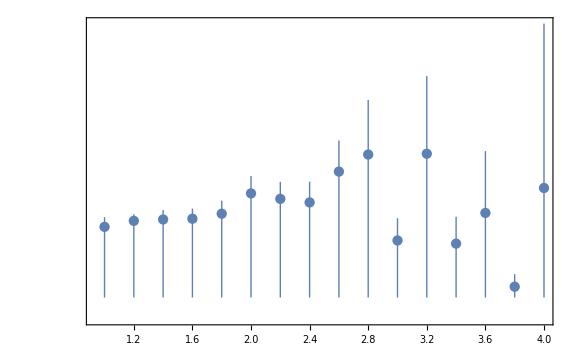

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

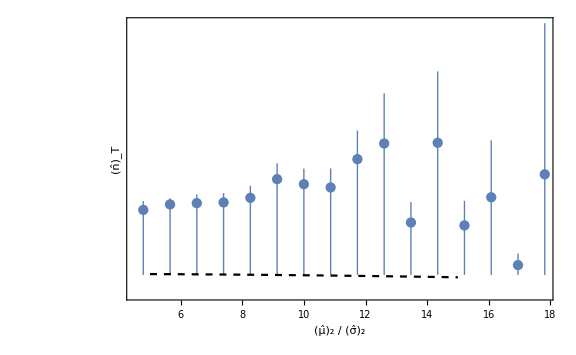

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

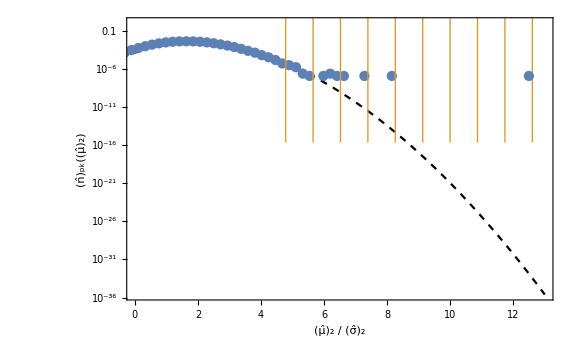

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

### s2 = 1

```mathematica
s2=1;
```

#### peak

```mathematica
mapdata=Import["data/LN"<>ToString[s2]<>"_map_0.csv"][[1]];
```

```mathematica
Length[mapdata]
```

16777216

```mathematica
Variance[mapdata]
```

0.569269

```mathematica
lapdata=Import["data/LN"<>ToString[s2]<>"_laplacian_0.csv"][[1]];
```

```mathematica
dn=2^2;
lap3D=Flatten[Table[{nx,ny,nz,lapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[lap3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/LN"<>ToString[s2]<>"_peak_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]];
```

```mathematica
lap2D=Flatten[Table[{ny,nz,lapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[lap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=1;
mukList=Flatten[Table[Import["data/LN"<>ToString[s2]<>"_peak_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[mu2_,k3_]=2/(6π)^(3/2)(σ2^2 σ4^3)/(σ1^4 σ3^3) mu2 k3 f[σ2/σ1^2 mu2]P13[σ2/σ1^2 mu2,σ2/σ1^2 mu2 k3^2];
nmu2PT[mu2_]=Integrate[npkPT[mu2,k3],{k3,0,∞},Assumptions->{mu2>0}];
```

```mathematica
1/(2π Sqrt[1-γ3^2])Exp[-(σ2^2/σ1^2 mu2)^2 1/2(1/σ2^2+1/(σ4^2(1-γ3^2))(σ4/σ2 k3^2-σ3^2/σ2^2)^2)]-P13[σ2/σ1^2 mu2,σ2/σ1^2 mu2 k3^2]//Simplify
```

0

```mathematica
σ2^2//N
```

70.8917

```mathematica
5.37 10^-11(2π)^4
```

8.36939×10^-8

```mathematica
kpeak=(2π npeak)/NL Sqrt[σ2/σ4]
```

1/ⅇ^6

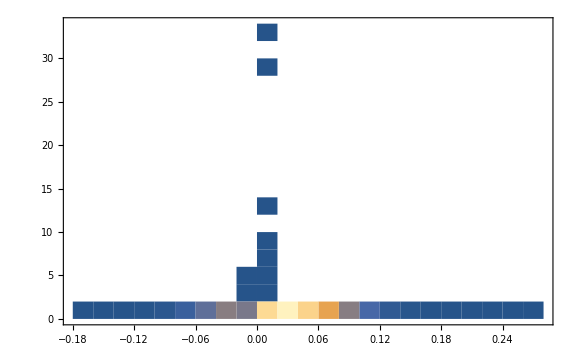

```mathematica
DensityHistogram[mukList,GridLines->{None,{kpeak}}]
```

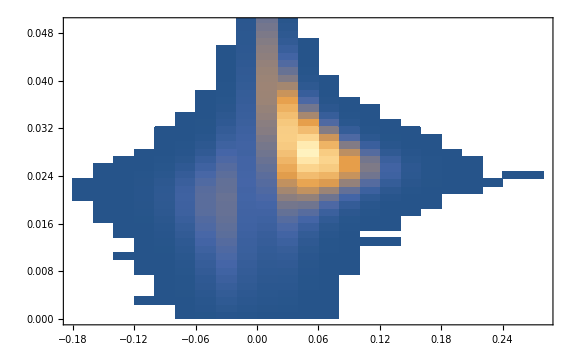

```mathematica
DensityHistogram[mukList,{Automatic,{kpeak/2}},GridLines->{None,{kpeak}},PlotRange->{Full,{0,20kpeak}}]
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

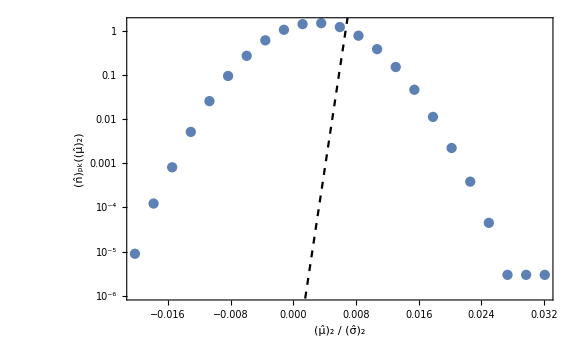

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,30},PlotStyle->{Dashed,Black}]]
```

```mathematica
HistoList=HistogramList[mukList,{1/10}];
```

```mathematica
Dmu2=HistoList[[1,1,2]]-HistoList[[1,1,1]];
Dk3=HistoList[[1,2,2]]-HistoList[[1,2,1]];
mu2min=Mean[HistoList[[1,1,1;;2]]];
k3min=Mean[HistoList[[1,2,1;;2]]];
npkLat=Flatten[Table[{mu2min+Dmu2(i-1),k3min+Dk3(j-1),Log10[HistoList[[2,i,j]]/(Dmu2 Dk3 Nsim NL^3)]},{i,Length[HistoList[[2]]]},{j,Length[HistoList[[2,1]]]}],1];
```

```mathematica
Show[ListDensityPlot[npkLat,PlotLegends->Automatic,InterpolationOrder->0,PlotRange->{{0,6},{0,5}}],
ContourPlot[Log10[npkPT[mu2,k3]],{mu2,0,6},{k3,0,5},ContourShading->None,Contours->{-3,-4,-5,-6,-7,-8},PlotRange->Full]]
```

-Graphics-

### test

```mathematica
mapdata=Import["data/LN0,1_map_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
```

1.01927

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->g[x,y,z]]]
```

-Graphics3D-

```mathematica
powerdata=Import["data/LN0,1_power_0.csv"][[1]];
```

```mathematica
powerList=Table[{i-1,powerdata[[i]]},{i,Length[powerdata]}];
```

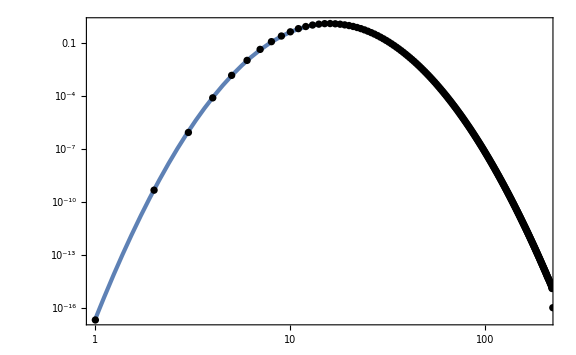

```mathematica
Show[LogLogPlot[1/Sqrt[2π 0.1] Exp[(-(Log[n]-Log[16])^2)/(2 0.1)],{n,1,200}],ListLogLogPlot[powerList,GridLines->{{npeak},None},FrameLabel->{n,Subscript[𝒫, g]},Joined->False,PlotStyle->Black]]
```

```mathematica
Length[powerdata]
```

443

```mathematica
biasedmap=Import["data/LN0,1_biased_0.csv"][[1]];
lapmap=Import["data/LN0,1_laplacian_0.csv"][[1]];
```

```mathematica
shiftedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
lapmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[lapmap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedlap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedlap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-